```mathematica
allprims=Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{PatternCanonicalize2[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[PatternCanonicalize2[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[$LifeData[#]])&,primitives]];
```

### Size of primitives over time

```mathematica
prims=ParallelSelect[$LifeData,If[#MatrixData["ExplicitLength"]<10^5,Length[CausalSeparation[#["MatrixData"]["ExplicitPositions"]]]==1,False]&];
```

```mathematica
primkeys = ;
```

```mathematica
BubbleChart[KeyValueMap[Append[#1, #2]&, Counts[{#Year, #InitialWeight}&/@ prims]], AspectRatio->.4, FrameLabel->{None, "size of pattern"}]
```

-Graphics-

```mathematica
GroupBy[Values[prims], (#Year&)->(#InitialWeight&)]
```

<|1969→{6,3,4,5,2,1,2,5,3,7,3,5,5,12},1970→{6,8,6,6,7,8,8,5,7,7,6,6,7,6,6,7,18,2,7,7,12,13,7,35,9,4,9,6,8,7,8,7,11,12,10,7,35,94,3,4,8,48,10,12,6,6,6,4,6,9,4,16,3,6},1971→{17,14,7,28,8,8,32,9,7,141,18,8,26,9,8,30,9,6,28,23,9,9,8,36,16,2,12,33,16,144,28,8,20,400,8,6,117,9,8,12,14,8,10,9,8},1972→{26,42,10,10,26,15,10,10,10,42,10,28,10,10,10,10,10,40,33,40,45,31,10,22,9,10,9,10,10,35,10,7,34,10,40,40,40,32,26,10,36,10,10,9,10,10,34,32},1973→{12,42,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,48,42,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,46,12,12,12,12,12,14,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,52,18,12,12,12,12,12,12,12,12,33,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,18,12,12,12,12},1976→{30,28,16},1977→{38,44,15,31,12,60,14},1978→{64},1979→{40},1980→{34,30,32},1982→{26,16},1984→{42},1985→{22},1988→{40,13,12},1989→{28,25,64,84,68,12,28,65,18,18,70,44,24,31,48,56,44},1990→{22,29},1992→{117,25,60,80,70,70,34,26,157,42,32,47,66,31,158,24,101,54,34},1993→{16,28,77,197,69,15,39,206,24},1994→{64,233,18,24,24,36,15,190,17,40,124,42},1995→{28,187,187},1996→{46,60,128},1997→{258,29,44,54,46,45,20,97,50,58,131},1998→{28,28,37,41,36,47},1999→{36,32,89},2000→{295,30,72,25,27,36,27},2001→{55,88,8,175,34,32},2002→{123,31,69},2003→{19,144,121},2004→{35,29,20},2005→{12,33,37,8,86,44,170,232},2006→{67,32,13},2008→{183,28},2009→{38,44,56},2010→{24,44,74,151,149,150},2011→{28,77,71,34,262,86},2012→{86},2013→{31,20,50},2014→{54,9,44},2015→{34,35,53},2016→{56,28,45,298,46,68},2017→{13,28,21},2018→{33,130,54,55,129,282},2019→{180,131,66,65},2020→{117,313,21,32},2021→{118,131,78,784,45,416},2022→{30,32,23,38,37,882,1078,92},2023→{31},2025→{58}|>

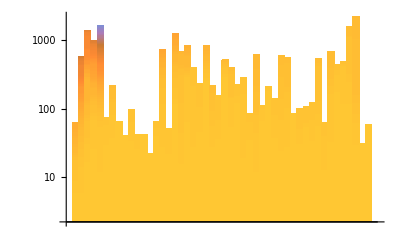

```mathematica
BarChart[GroupBy[Values[prims], (#Year&)->(#InitialWeight&)], ChartLayout->"Stacked", ScalingFunctions->"Log"]
```

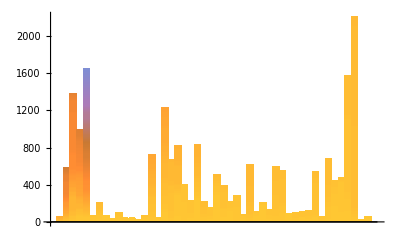

```mathematica
BarChart[GroupBy[Values[prims], (#Year&)->(#InitialWeight&)], ChartLayout->"Stacked"]
```

### Inverse moore’s law for primitives

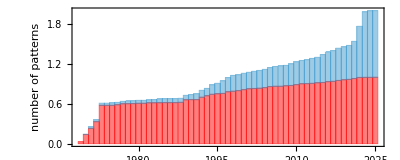

```mathematica
Histogram[Reverse@{KeyComplement[{#Year&/@ $LifeData,#Year&/@prims}], #Year&/@prims}, {1},"CDF",AspectRatio->.4,Frame->True,ChartStyle->Reverse@{ColorData["DefaultPlotColors"][1],Red},FrameLabel->{None,"number of patterns"},ChartLayout->"Stacked"]
```

Should really add up to 1 but you get the point

### Highlighting primitives in all patterns

#### Dev

```mathematica
Function[name, With[{pat = $LifeData[#, "MatrixData"]},
 ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->50]&[
intersectingidxs[pat, #]&[
PatternCanonicalize2/@Table[CellularAutomaton["GameOfLife", {#MatrixData, 0},{{{i}}}], {i, 0, Replace[#[["Period"]],_Missing->1] - 1}]&[$LifeData[name]]
]
]]&/@Take[names[[Catenate[Position[matall[[Position[names, name][[1, 1]]]], 1]]]], UpTo[10]]]/@byrank[[;;5]]
```

```mathematica
highlightintersecting[sa1_, sa2_]:= 
ArrayPlot[ReplacePart[sa1, 
Thread[#->Red]], ImageSize->50]&[

intersectingidxs@@@(CanonicalIdxs[#["ExplicitPositions"]]&/@ {sa1, sa2})]
```

```mathematica
highlightintersecting[$LifeData["Gosper glider gun", "MatrixData"], $LifeData["Block", "MatrixData"]]
```

-Graphics-

```mathematica
intersectingidxs@@(CanonicalIdxs[#["ExplicitPositions"]]&/@ {$LifeData["Gosper glider gun", "MatrixData"], $LifeData["Block", "MatrixData"]})
```

{{{1,12},{2,14},{2,12},{3,24},{3,23},{3,16},{3,15},{3,2},{3,1},{4,25},{4,21},{4,16},{4,15},{4,2},{4,1},{5,36},{5,35},{5,26},{5,20},{5,16},{5,15},{6,36},{6,35},{6,26},{6,22},{6,20},{6,19},{6,14},{6,12},{7,26},{7,20},{7,12},{8,25},{8,21},{9,24},{9,23}},{{1,1},{2,1},{1,2},{2,2}}}

```mathematica
Function[{s1, s2}, ]
```

```mathematica
intersectingidxs[Normal@$LifeData["Gosper glider gun", "MatrixData"], {Normal@$LifeData["Block", "MatrixData"]}]
```

{{{5,1},{5,2},{6,1},{6,2}},{{3,35},{3,36},{4,35},{4,36}}}

```mathematica
intersectingidxs2[pat_, subpat_]:=  
Select[
CausalSeparation[pat["ExplicitPositions"]], # === subpat&]
```

```mathematica
Function[{pat, subpat}, 
ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->50]&[
Function[{patidxs, subpatidxs}, Select[
CausalSeparation[patidxs], CanonicalIdxs[#] ===subpatidxs&]][pat["ExplicitPositions"],CanonicalIdxs[subpat["ExplicitPositions"]]]]][$LifeData["Gosper glider gun", "MatrixData"], 
$LifeData["Block", "MatrixData"]]
```

-Graphics-

```mathematica
Values[#MatrixData&/@ prims][[1]]
```

SparseArray[…]

```mathematica
g = GroupBy[Values@$LifeData, #Year&];
```

```mathematica
Function[{pat, subpats}, 
ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->{40, 40}]&[
Function[{patidxs, subpatidxs}, Select[
CausalSeparation[patidxs], MemberQ[subpatidxs, CanonicalIdxs[#]]]][pat["ExplicitPositions"],CanonicalIdxs[#["ExplicitPositions"]]&/@subpats]]][$LifeData["Block", "MatrixData"], Values[#MatrixData&/@ prims]]
```

-Graphics-

```mathematica
Function[name, With[{pat = $LifeData[#, "MatrixData"]},
 ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->50]&[
```

```mathematica
CanonicalIdxs/@CausalSeparation[$LifeData["Gosper glider gun", "MatrixData"]["ExplicitPositions"]]
```

{{{1,6},{1,5},{2,7},{2,3},{3,8},{3,2},{4,8},{4,4},{4,2},{4,1},{5,8},{5,2},{6,7},{6,3},{7,6},{7,5}},{{1,1},{2,3},{2,1},{3,5},{3,4},{4,5},{4,4},{5,5},{5,4},{6,3},{6,1},{7,1}},{{1,1},{2,1},{1,2},{2,2}},{{1,1},{2,1},{1,2},{2,2}}}

#### Running

```mathematica
Map[
ParallelMap[
Function[{pat, subpats}, 
If[pat["MatrixData"]["ExplicitLength"]<10^5, 
ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->{40, 40}]&[
Function[{patidxs, subpatidxs}, Select[
CausalSeparation[patidxs], MemberQ[subpatidxs, CanonicalIdxs[#]]&]][pat["ExplicitPositions"],CanonicalIdxs[#["ExplicitPositions"]]&/@subpats]]],
TooBig][
#MatrixData, Values[#MatrixData&/@ prims]
]&,#]&,g[[;;3]]]
```

<|1969→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1970→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1971→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Function[{pat, subpats}, 
If[pat["ExplicitLength"]<10^5, 
ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->{100, 100}]&[
Function[{patidxs, subpatidxs}, Select[
CausalSeparation[patidxs], MemberQ[subpatidxs, CanonicalIdxs[#]]&]][pat["ExplicitPositions"],CanonicalIdxs[#["ExplicitPositions"]]&/@subpats]],
TooBig]][
#MatrixData, Values[#MatrixData&/@ prims]
]&/@RandomSample[Values[Select[$LifeData, #Year ==2023&]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[1111];
Function[{pat, subpats}, 
If[pat["ExplicitLength"]<10^5, 
ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->{100, 100}]&[
Function[{patidxs, sps}, 
Select[
CausalSeparation[patidxs], MemberQ[Normal/@sps, PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]]&]][pat["ExplicitPositions"],subpats]],
TooBig]][
SparseArray[PatternCanonicalize2[ResourceFunction["ArrayCrop"][#MatrixData]]], Values[#MatrixData&/@ prims]
]&/@RandomSample[Values[Select[$LifeData, #Year ==2023&]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[{patidxs, sps}, 
Select[
CausalSeparation[patidxs], MemberQ[Echo[sps[[;;3]]], PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]]&]][$LifeData["Gosper glider gun", "MatrixData"]["ExplicitPositions"],Values[#MatrixData&/@ prims]]
```

{SparseArray[…],SparseArray[…],SparseArray[…]}

{SparseArray[…],SparseArray[…],SparseArray[…]}

{SparseArray[…],SparseArray[…],SparseArray[…]}

«1 more identical outputs»

{}

```mathematica
SparseArray[PatternCanonicalize2[ResourceFunction["ArrayCrop"][#MatrixData]]&[$LifeData["Gosper glider gun"]]]
```

SparseArray[…]

### New parts

```mathematica
g = GroupBy[Values@$LifeData, #Year&];
```

```mathematica
g[[1, 1]]
```

<|Name→Beehive,Year→1969,Class→Strict still life,Wiki→https://conwaylife.com/wiki/Procrastinator,DataFiles→{beehive.cells,beehive.rle},MatrixData→SparseArray[Automatic,{3,4},0,{1,{{0,2,4,6},{{2},{3},{1},{4},{2},{3}}},{1,1,1,1,1,1}}],InitialWeight→6|>

```mathematica
Function[{pat, subpats}, 
If[pat["ExplicitLength"]<10^5, 
Function[{patidxs, subpatidxs}, 
Select[CausalSeparation[patidxs], MemberQ[subpatidxs, CanonicalIdxs[#]]&]][pat["ExplicitPositions"],CanonicalIdxs[#["ExplicitPositions"]]&/@subpats
],TooBig]][g[[1, 1]]["MatrixData"], Values[#MatrixData&/@ prims]]
```

{{{1,2},{1,3},{2,1},{2,4},{3,2},{3,3}}}

This is taking too long but will be interesting

```mathematica
newbits = ParallelMap[
Function[{pat, subpats}, 
If[pat["ExplicitLength"]<10^5, 
Function[{patidxs, subpatidxs}, Select[
CausalSeparation[patidxs], KeyExistsQ[subpatidxs, CanonicalIdxs[#]]&]][pat["ExplicitPositions"],Association[CanonicalIdxs[#["ExplicitPositions"]]->1&/@subpats]
],TooBig]][#MatrixData, Values[#MatrixData&/@ prims]]&/@ #&,g];
```

$Aborted

```mathematica
resall = ;
```

```mathematica
oresall = ;
```

```mathematica
xresall = ;
```

```mathematica
allparts=ParallelMap[{#Name,#["Year"],If[#["MatrixData"]["ExplicitLength"]<10^5,CanonicalParts[Normal[#["MatrixData"]]],TooBig]}&,$LifeData];
```

$Aborted

```mathematica
xresall[[;;5]]
```

<|Beehive→{None},Blinker→{None},Block→{None},Crotchet→{None},Domino→{None}|>

```mathematica
PieChart[{1, 2}]
```

-Graphics-

```mathematica
Take[GroupBy[Normal[xresall], $LifeData[#[[1]]]["Year"]&], 1]
```

<|1969→{Beehive→{None},Blinker→{None},Block→{None},Crotchet→{None},Domino→{None},Dot→{None},Duoplet→{None},Glider→{None},Line of three→{Blinker},Loaf→{None},Pre-block→{None},R-pentomino→{None},Short table→{None},Traffic light→{None}}|>

```mathematica
Map[PieChart[#, ImageSize->40]&,RandomSample[Values[Quiet[ReplaceAll[With[{ccc = Count[#, None]}, {ccc, Length[#] - ccc}]&/@ xresall, Indeterminate->0]]], 3]&/@ (#[[All, 2]]&/@Take[GroupBy[Normal[xresall], $LifeData[#[[1]]]["Year"]&], 1]), {2}]
```

<|1969→{-Graphics-,-Graphics-,-Graphics-}|>

### Better histogram

```mathematica
Quiet[ReplaceAll[With[{ccc = Count[#, None]}, {ccc, Length[#] - ccc}]&/@ xresall, Indeterminate->0]]
```

```mathematica
GroupBy[ContainsOnly[#, {None}]&/@ xresall,
```

```mathematica
GroupBy[Keys[xresall], $LifeData[#, "Year"]&]
```

<|1969→{Beehive,Blinker,Block,Crotchet,Domino,Dot,Duoplet,Glider,Line of three,Loaf,Pre-block,R-pentomino,Short table,Traffic light},1970→{Aircraft carrier,Banana spark,Barge,Beacon,B-heptomino,Bi-block,Bipole,Blockade,Boat,Bookend,Bun,Cavity,Century,C-heptomino,Claw,Clock,Crinkly heptomino,Cuphook,Diagonal on-off,E-heptomino,F-heptomino,Figure eight,Gosper glider gun,Heavyweight spaceship,Herschel,Hertz oscillator,Honey farm,House,Leg,Lightweight spaceship,Line-of-six spark,Long barge,Long boat,Long ship,Long snake,Middleweight spaceship,Pentadecathlon,Period-60 glider gun,Phi spark,Pi-heptomino,Pinwheel,Pole 2,Pole 3,Pole 4,Pond,Pulsar,Quadpole,Queen bee,Queen bee shuttle,Ship,Snake,Table,Tail,Toad,Tripole,Tub,Tumbler,V spark,Z-hexomino},1971→{3c/10 pi wave,Almosymmetric,Big S,Block-laying switch engine,Blonk-tie,Boat-bit,Candelabra,Canoe,Cap,Cauldron,Cis-boat with tail,Double ewe,Eater 1,Ecologist,Flutter,French kiss,Gliders by the dozen,Gray counter,Hat,Hook with tail,Hustler,Integral sign,Interchange,Iwona active region,Kok's galaxy,Light bulb,Long canoe,Long.b3 snake,Mango,Negentropy,New gun 1,Noah's ark,Octagon 2,Orthogonal on-off,p60 glider shuttle,Phoenix 1,Pi ship 1,Piston,Pressure cooker,Puffer 1,Quad,Quasar,Scrubber,Shillelagh,Spark coil,Spiral,Squaredance,Switch engine,Thunderbird,Titanic toroidal traveler,Trans-boat with tail,Tub with tail,Twin bees shuttle,Twin bees shuttle spark,Two eaters,Two-glider octomino,U-turner,Very long boat,Very long snake,Washerwoman},1972→{1-2-3,Airforce,Barge siamese loaf,Beehive with tail,Biting off more than they can chew,Block on griddle,Block on table,Boat-tie,Boat with long tail,Boss,Broken snake,Burloaferimeter,Carrier siamese carrier,Cis-barge with tail,Cis-shillelagh,Cis-very long hook with tail,Claw with tail,Diamond ring,Dinner table,En retard,Four skewed blocks,Frog II,Germ,Hooked integral,Loading dock,Long hook with tail,Long integral,Long shillelagh,Long⁴ snake,Loop,Mathematician,Melusine,Multum in parvo,Penny lane,Prodigal,Protein,Pyrotechnecium,RF28B,Roteightor,Schick engine,Snacker,Snake dance,Snake pit,Snake siamese snake,Sombreros,Surprise,Trans-barge with tail,Trans-very long hook with tail,Tub with long tail,Tub with very long tail,Two-glider mess,Very long shillelagh,Worker bee,$rats},1973→{Asymmetric amphisbaena,aVerage,Barge with very long tail,Beehive at beehive,Beehive at claw,Beehive on table,Beehive with hooked tail,Beehive with nine,Block on cap,Block on cover,Boat tie eater head,Boat tie eater tail,Boat tie long boat,Boat tie long snake,Broken elevener,Bun with feather,Canoe siamese snake,Carrier bridge carrier,Carrier bridge snake,Carrier bridge table,Carrier siamese canoe,Carrier siamese hook-with-tail hook,Carrier siamese hook-with-tail tail,Carrier siamese shillelagh,Carrier siamese tub with tail,Carrier siamese very long snake,Carrier tie ship,Chemist,Circle of fire,Cis-barge with nine,Cis-block on long bookend,Cis-boat amphisbaena,Cis-boat trans-line tub,Cis-boat with long.b3 tail,Cis-carrier down on table,Cis-carrier-tie,Cis-carrier tie snake,Cis-carrier up on table,Cis-fuse with two tails,Cis-long barge with tail,Cis-long⁴ hook with tail,Cis-mango with tail,Cis-ship on table,Cis-snake-tie,Cis-tub with long⁴ tail,Cis-very long hook with nine,Claw at claw,Claw siamese tub with cape,Claw with boat with tail,Claw with nine,Crowd,Double claw,Down snake on table,Eater head siamese eater head,Eater head siamese eater tail,Eater head siamese long snake,Eater plug,Eater tail siamese eater tail,Eater tail siamese long snake,Eater with head feather,Eater with tail feather,Egyptian walk,Fuse with tail and nine,Fuse with tail and very long tail,Fuse with two long tails,Gull with tub,Honeybarge,Hook-with-tail hook siamese snake,Hook-with-tail tail siamese snake,Hook with tail with cape,Hook with two tails,Inflexion,Integral with hook and tail,Integral with tub and tail,Long boat with long tail,Long hook line tub,Long.b3 integral,Long integral with boat,Long snake siamese long snake,Long snake with feather,Long tub-claw with tail,Mazing,Newshuttle,p54 shuttle,Pedestle,Pulsar quadrant,Rotated table,Shillelagh siamese snake,Ship tie snake,Siesta,Snake bridge snake,Snake siamese very long snake,Snorkel loop,Teardrop with cape,Teardrop with claw,Technician,Trans-barge with nine,Trans-block on long bookend,Trans-boat amphisbaena,Trans-boat trans-line tub,Trans-boat with long.b3 tail,Trans-carrier down on table,Trans-carrier-tie,Trans-carrier tie snake,Trans-carrier up on table,Trans-long barge with tail,Trans-mango with tail,Trans-ship on table,Trans-snake-tie,Trans-tub with long⁴ tail,Trans-very long hook with nine,Tub bend line tub,Tub with tail siamese snake,Tub with tail with cape,Tub with two down cis tails,Tub with two down trans tails,Tub with two up cis tails,Tub with two up trans tails,Twelve loop,Two pulsar quadrants,Up snake on table,Very long claw with tail,Very long melusine,Very long prodigal},1976→{Buckingham's p13,Extremely impressive,Pentant,Unix,p8honeyfarmhassler},1977→{38P11.1,44P7.2,Blinkers bit pole,Eater 3,Four eaters hassling lumps of muck,Fox,Pentoad,Tritoad,Why not},1978→{Gourmet,Harbor,Sixty-nine},1979→{Octagon 4},1980→{Eureka,Heavyweight emulator,Lightweight emulator,Middleweight emulator,p29 pre-pulsar shuttle},1982→{Heart,p47 pre-pulsar shuttle,Trice tongs},1983→{p10 traffic light hassler,p26 pre-pulsar shuttle,Tumbling T-tetson,Two pre-L hasslers},1984→{6 bits,Blinker puffer 1,Carnival shuttle,Hectic,Jack,p36 toad hassler,Sailboat,p11honeyfarmhasslers,p9lumpsofmuckhassler},1985→{Pulshuttle V,Stillater},1986→{p55 pre-pulsar hassler},1988→{Achim's p4,Jam,Mold},1989→{106P135,119P4H1V0,1-2-3-4,25P3H1V0.1,64P2H1V0,84P3H1V0.1,Baker's dozen,Bent keys,Big glider,Caterer,Cross,Double caterer,Fumarole,Monogram,Odd keys,Short keys,Skewed traffic light,Statorless p6,Tempest,T-nosed p4,Triple caterer,Turning toads,Turtle,Twirling T-tetsons 2,Windmill},1990→{22P4.3,Loaflipflop,New five,Two blockers hassling R-pentomino},1991→{44P5H2V0},1992→{117P9H3V0,20P4,25P3H1V0.2,60P3H1V0.3,70P2H1V0.1,70P5H2V0,Blinker puffer 2,Brain,Dart,Edge-repair spaceship 1,Fly,Hivenudger,Hivenudger 2,Laputa,Middleweight volcano,Non-monotonic spaceship 1,p44 pi-heptomino hassler,p50 glider shuttle,Pushalong 1,Ring of fire,Sidecar,Sparky,Toaster,Wickstretcher 1,x66},1993→{2.3.3,A for all,Boatstretcher 1,Bracket pulsar,Bracket quasar,Cross 2,Electric fence,Enterprise,Glider pusher,Muttering moat 1,Orion,Slow puffer 2,Spacefiller 1,Star,Wing (spaceship),p129piheptominohassler2},1994→{101,134P25,186P24,233P3H1V0,Achim's other p16,Achim's p11,Achim's p144,Achim's p16,Achim's p8,Bottle,Crown,Fore and back,Fountain,Four blinkers around four blocks,Jason's p6,Metamorphosis II,New gun 2,p124 lumps of muck hassler,p42 glider shuttle,p48 toad hassler,p50 traffic jam,p58 toadsucker,Pseudo-barberpole,Rumbling river 1,Ship in a bottle,Smiley,T-nosed p6,Traffic circle,Trivial p6-1,Twin bees shuttles hassling blinker,Vex,36p8sparker,prepulsarshuttle40},1995→{124P21,145P20,22P36,Coe ship,Four molds hassling eight blocks,Heavyweight volcano,Max,p156 Hans Leo hassler,p18 bi-block hassler,p35 beehive hassler,p60 traffic light hassler,Period-256 glider gun,Pi orbital,R64,Spacefiller 2,Zweiback,p12rpentominohasslers,prepulsarshuttle32},1996→{46P4H1V0,49P88,60P5H2V0,B-52 bomber,Conduit 1,F117,Fx119,Fx119 inserter,Fx158,Fx77,Glider stopper,Glider to block,Herschel receiver,L112,L156,p52 R-pentomino hassler,Period-184 glider gun,Period-246 glider gun,Period-690 glider gun,R190,RR56H,Snail,Swan,p79picenturyhassler},1997→{168P22.1,258P3,258P3 on Achim's p11,29P9,44P14,54P17.1,Babbling brook 1,Champagne glass,Coe's p8,Elkies' p5,F116,F166,Fx153,Fx176,Hebdarole,Herschel transmitter,HF95P,HFx58B,Lx200,p15 pre-pulsar spaceship,p6 pipsquirter,Period-24 glider gun,Period-44 glider gun,Period-44 MWSS gun,PF35W,RF48H,Rx202,Spider,Vacuum (gun),Waveguide 1,prepulsarshuttle42},1998→{28P7.1,28P7.2,37P10.1,41P7.2,Bx125,Bx222,Callahan G-to-H,Diuresis,p5 bouncer,p6 bouncer,p8 bouncer,Pre-pulsar spaceship,RNE-19T84,Superfountain,Thumb 1,Wasp,p15piheptominohassler2,prepulsarshuttle60},1999→{Canada goose,Glider emulator,Orion 2,p7 pipsquirter},2000→{134P39.1,295P5H1V1,30P5H2V0,72P6H2V0,Crab,Dragon,Edge-repair spaceship 2,Jason's p22,Jason's p33,p6 thumb,Period-22 glider gun,Silver's p5,Weekender,Wings},2001→{55P9H3V0,Backrake 1,Boojum reflector,Coolout Conjecture,Frothing puffer,p130 shuttle,Quad pseudo still life,Triple pseudo still life},2002→{123P27.1,31P8H4V0,50P35,69P48,98P25,Blom,Four eaters hassling four bookends,Gabriel's p138,Karel's p15,p15 bouncer,p24 shuttle},2003→{(13,1)c/31 Pseudo-B climber,Fire-spitting,Jason's p11,p4 pipsquirter,p60 B-heptomino hassler},2004→{160P10H2V0,35P4H1V1,3-engine Cordership,B29,Blonker,Iwona,Jason's p36,Justyna,p6 shuttle,Period-156 glider gun,p12honeyfarmhassler,p36lumpsofmuckhassler},2005→{23334M,33P4H1V1,37P7.1,7468M,86P5H1V1,94P27.1,Crane,Lidka,One per generation,p72 quasi-shuttle,Seal,Switch engine channel,T-nosed p5},2006→{274P6H1V0,67P5H1V1,Cyclic,Demultiplexer,F171,Honeybit,Ship+fishhook,Sidewinder},2007→{52P84,78P70,Four eaters,Karel's p177,Karel's p28,Land of lakes,p25 pre-pulsar shuttle,p24rpentominohassler},2008→{35201M,Bulldozer,Eve,Scot's p5,prepulsarshuttle36},2009→{128P10.2,38P7.2,44P12.3,46P10,48P22.1,56P6H1V0,68P32,Beluchenko's p13,Beluchenko's p37,Beluchenko's p40,Beluchenko's p51,p11 pinwheel,Period-88 glider gun,Rectifier},2010→{110P62,24P10,32829M,44P10,56P27,58P5H1V1,74P8H2V0,Beluchenko's other p37,Ed,Edna,Ellison p4 HW emulator,Fred,Merzenich's p11,Merzenich's p31,Merzenich's p64,p32 blinker hassler,p32 blinker hassler 2,p44 traffic light hassler,Period-45 glider gun},2011→{5blink,77P6H1V1,G4 receiver,Glider to 2 blocks,Lobster,Merzenich's p18,Montana,p11 double-length signal injector,p48 pi-heptomino hassler,R126,Swine},2012→{37P4H1V0,86P6H3V0,HLx111R,p26 dependent reflector loop,p31 dependent reflector loop,Statorless p3,p70vsparker,p55prepulsarshuttle},2013→{135-degree MWSS-to-G,31.4,31c/240 Herschel-pair climber,AK-94,CC semi-Snark,Century eater,Loafer,Period-20 glider gun,Pi splitter,Snark,50p8sparker,prepulsarshuttle22},2014→{50P9,65P48,90P51,c/12 R-pentomino crawler,Honey thieves,Jaydot,Pufferfish,Pufferfish spaceship,p55piheptominohassler2},2015→{34P5H2V0,35P12.1,45-degree MWSS-to-G,50P92.1,53P13,B60,Beehive stopper,BLx19R,BNE14T30,BRx46B,CBx37C,HL75P,H-to-MWSS,Ocellus,p18 honey farm hassler,p29 traffic-farm hassler,p58 pre-pulsar shuttle,Sidesnagger,Simkin glider gun,Simkin's p60,SW1T43,Syringe,p22honeyfarmhassler,p22lumpsofmuckshuttle,prepulsarshuttle64,prepulsarshuttle88,prepulsarshuttle90},2016→{112P15,132P7,600P6H1V0,84P87,Cloverleaf interchange,Copperhead,Cthulhu,Fireship,Grandfather problem,p21 honey farm hassler,p28 pre-pulsar shuttle,p35 honey farm hassler,p4 bumper,p5 bumper,p6 bumper,p7 bumper,p8 bumper,p9 bumper,Professor,Rattlesnake,Rich's p16,Scorbie Splitter,Spaghetti monster,Statorless p5},2017→{24827M,28P7.3,2-engine Cordership,339P7H1V0,CC semi-cenark,CP semi-cenark,CP semi-Snark,F131,p46 gliderless MWSS gun,Period-92 glider gun,Quadri-Snark,Runny nose,Tanner's p46,Tremi-Snark},2018→{209P8,33P3.1,34P14 shuttle,42100M,54P3H1V0,55P10,68P16,68P9,Bronco,Cottonmouth,Homer,Jormungant's G-to-H,MWSS behind Coe ship,p36 shuttle,p3 bumper,p46 gliderless LWSS gun,p4 bouncer,p5 pipsquirter,p64 thunderbird hassler,p9 bouncer,Period-33 glider gun,Sir Robin,Wilma,p36honeyfarmhassler,p36honeyfarmhassler2,p40honeyfarmhassler,p80pihassler},2019→{180P8,47575M,64P6,66P13,74P85,David Hilbert,Dueling banjos,R49,Scholar,tnosep8sparker,p13piheptominowick,p12lumpsofmuckhassler},2020→{104P9,186P7H2V0,409P6H1V0,49768M,Anura,Bandersnatch,Beehive push catalyst,Doo-dah,L122,p143 Bandersnatch loop,Rob's p16,Soba,Unnamed tagalong 23P4H2V0},2021→{50093M,52513M,62P7,66P62,72P21,754P7,Gallus,Nihonium,p11 bouncer,p11 domino sparker,p128 wing shuttle,p196 pi-heptomino hassler,p21 B-heptomino hassler,p32 honey farm hassler,p3 pipsquirter,p486 R-pentomino hassler,p4 syringe,p576 R-pentomino hassler,p76 pi-heptomino hassler,p96 honey farm hassler,Period-117 glider gun,Period-144 glider gun,Period-54 glider gun,Period-55 glider gun,Raucci's p74,T-nosed p7,Traffic stop,p9honeyfarmhassler,p147honeyfarmhassler,p52honeyfarmhassler,p31rpentominohassler,p32rpentominohassler,p35rpentominohassler2,p50rpentominohassler,p57rpentominohassler,p60rpentominohassler,p60rpentominohassler2,p13piheptominohassler,p182pihassler,p75lumpsofmuckhassler,p138lumpsofmuckhassler,p12blonktiehassler,prepulsarshuttle35,prepulsarshuttle36reduced,prepulsarshuttle65},2022→{112P57,120P34,20-cell quadratic growth,232P7H3V0,255P132,30P25,30P3,32P21,32P4H2V0,34P20,34P7,35P12H6V0,36P25,42P14,43P54,52P44,54P94,55P23,58P37,58P8H4V0,62P83,66P106,70P23,70P26,74P127,74P34,76P86,84P199,92P23,92P59,Charity's p16,Chucklebait,CL48C,Diamondback,Grid's p16,HRx65R,HRx74B,Meatball,NW-2T16,P10 domino fountain,p111 R-pentomino hassler,p112 puffer,p11 thumb,p129 R-pentomino hassler,p146 pi-heptomino hassler,P16-assisted period-32 glider gun,p23 honey farm hassler,p28 block puffer,p39 pi-heptomino hassler,p43 pi-heptomino hassler,p45 pi-heptomino hassler,p49 R-pentomino hassler,p4-assisted period-28 glider gun,p58 pi-heptomino hassler,p59 dependent reflector loop,P6 domino fountain,p6 honey farm hassler,p71 honey farm hassler,p73 lumps of muck hassler,p75 I-heptomino hassler,p79 pi-heptomino hassler,p82 pi-heptomino hassler,p84 honey farm hassler,p85 R-pentomino hassler,p86 R-pentomino hassler,p8 glider reflector,p94 R-pentomino hassler,Period-113 glider gun,Period-25 glider gun,Period-27 glider gun,Period-34 glider gun,Period-43 glider gun,Period-48 glider gun,Period-51 glider gun,Raucci's p102,Raucci's p38,Speed tunnel,Taco,Twin bees shuttle on 21P4.1,Unique father problem,Unsynthesizable oscillator 1,p10lonedotsparker,p7honeyfarmhassler,p9honeyfarmhassler3,p10honeyfarmhassler,p12honeyfarmsparker,p12honeyfarmhassler3,p27bananasparker,p33honeyfarmhassler2,p34honeyfarmhassler,p43honeyfarmhassler,84p51,p51honeyfarmhassler,p52honeyfarmhassler2,p52honeyfarmhassler3,p54honeyfarmandbhassler,p56honeyfarmhassler,p62honeyfarmhassler,p64honeyfarmhassler,p64honeyfarmhassler2,p72honeyfarmhassler,p72honeyfarmhassler2,cappedp74gun,p77honeyfarmhassler,p90honeyfarmhassler,p90honeyfarmhassler2,p91honeyfarmhassler,p96honeyfarmhassler2,p100honeyfarmhassler2,p102honeyfarmhassler,p108honeyfarmhassler,p120honeyfarmhassler,p128honeyfarmhassler,p143honeyfarmhassler,p30honeyfarmshuttle,p32doubleshuttle,p36honeyfarmhassler6,p36honeyfarmshuttlejp21,p38honeyfarmshuttle,p40andp50dominofountains,p48honeyfarmhassler,p60honeyfarmshuttle,p60honeyfarmshuttle2,p220honeyfarmshuttle,p8rpentominohassler,p23rpentominohassler,p30rpentominohassler,p30rpentominohassler2,p32rpentominohassler2,p35rpentominohassler,p38rpentominohassler,p45rpentominohassler,p49singlerpentominohassler,p64rpentominohassler2,p90rpentominohassler,p104rpentominohassler,p109rpentominohassler,p112rpentominohassler,p120rpentominohassler,p122rpentominohassler,p140rpentominohassler,cappedp140gun,p146rpentominohassler,p147rpentominohassler,p150rpentominohasslerglidergun,p166rpentominohassler,p253rpentominohassler,p18piheptominohassler,p46piheptominohassler,p61piheptominohassler,p68piheptominohassler,p70piheptominohassler,p72lumpsofmuckhassler,p77pihassler,p92piheptominohassler,p95piheptominohassler,p100piheptominohassler,p64andp128piheptominohasslers,p160piheptominoshuttle,p186pihassler,p25lumpsofmuckhassler,p27lumpsofmuckhassler,p35lumpsofmucksparker,p35lumpsofmuckhassler,p37lumpsofmuckhassler,p40lumpsofmuckhassler,p40lumpsofmuckhassler2,p46lumpsofmuckhassler,p49lumpsofmuckhassler,p51lumpsofmuckhassler,p68lumpsofmuckhassler,p76lumpsofmuckhassler,p80singlelumpsofmuckhassler,p80lumpsofmuckhassler,p100lumpsofmuckhassler,p104lumpsofmuckshuttle,p140lumpsofmuckhassler,p184lumpsofmuckhassler,p28centuryhassler,p28centuryshuttle,p110centuryshuttle,cl48cloop,p80twinbeesshuttle,p36winghassler,p48longbunhassler,p16uturnerhassler,p48prepulsarshuttle},2023→{0-degree colour-preserving reflector (March 2023),112P23,116P101,32P21 phase-shifting p5,42P38,44P49,51P384,72P119,86P107,94P53,Charity's p25,Charity's p30,Cribbage,G-to-pi catalyst (August 2023),Mold on fire-spitting,Odd traffic stop,p126 R-pentomino hassler,p13 domino sparker,p140 two-glider octomino hassler,p16 century shuttle,p17 R-pentomino hassler,p224 lumps of muck hassler,p24 gliderless LWSS gun,p26 honey farm hassler,p280 U-turner hassler,p41 pi-heptomino hassler,p47 lumps of muck hassler,p49 pi-heptomino hassler,p59 pi-heptomino hassler,p67 B-heptomino hassler,p68 century hassler,p76 pi-heptomino shuttle,p82 lumps of muck hassler,p93 R-pentomino hassler,Period-201 glider gun,Period-49 glider gun (April 2023),Period-61 glider gun (2023),Snark64,Walrus,p9honeyfarmhassler2,p12honeyfarmhassler2,p27honeyfarmhassler,p27d2honeyfarmhassler,p34mod17honeyfarmhassler,p39honeyfarmhassler,p44honeyfarmhassler2,p46honeyfarmhassler2,p46longbunhassler,p47honeyfarmhassler,p49honeyfarmhassler,p52honeyfarmhassler4,p56c2honeyfarmhassler,p58honeyfarmhassler,p65honeyfarmhassler,p65honeyfarmhassler2,p66honeyfarmhassler,p69honeyfarmhassler,p70honeyfarmhassler,p73honeyfarmhassler,p75honeyfarmhassler,p77honeyfarmhassler2,p80honeyfarmhassler,p80honeyfarmhassler2,cappedp91gun,p96honeyfarmhassler3,p97honeyfarmhassler,p110honeyfarmhassler,p110honeyfarmhassler2,p110honeyfarmhassler3,p120honeyfarmhassler2,p130honeyfarmhassler,p182honeyfarmhassler,p38honeyfarmshuttle2,p40honeyfarmhassler4,p40honeyfarmshuttle,p44honeyfarmhassler,p136honeyfarmshuttle,p13rpentominohassler,p24rpentominohassler2,p35rpentominohassler3,p54rpentominohassler,p76rpentominoshuttle,p78rpentominohassler,p86rpentominohassler2,p88rpentominoshuttle,p88rpentominohassler,p96rpentominohassler,p102rpentominohassler,p105rpentominohassler,p127rpentominohassler,p135rpentominohassler,p140rpentominoshuttle,p150rpentominohassler,p156rpentominohassler,p175rpentominohassler,98p201,p14piheptominohassler,p20piheptominohassler,p25piheptominohassler,p33piheptominohassler,p36piheptominohassler,p36piheptominohassler2,p39piheptominohassler2,p39c4piheptominohassler,p46piheptominohassler2,p47piheptominohassler,p52piheptominohassler,p53piheptominohassler,p53piheptominohassler2,p60piheptominohassler,p60piheptominohassler2,p65piheptominohassler,p68piheptominohassler2,p69piheptominohassler,p70piheptominohassler3,p72piheptominohassler2,p76piheptominohassler4,p78piheptominohassler,p78piheptominohassler2,p79piheptominohassler2,p88piblonktiehassler,p90piheptominohassler,p108piheptominohassler,p112piheptominohassler2,p117piheptominohassler,p121piheptominohassler,p125piheptominohassler2,p126piheptominohassler3,p128piheptominohassler2,p129piheptominohassler,p132piheptominohassler2,p158piheptominohassler,p159piheptominohassler,p13lumpsofmuckhassler,p21lomhassler2,p25singlelumpsofmuckhassler,p34lumpsofmuckhassler,p42lumpsofmuckhassler,p42lumpsofmuckshuttle,p42lumpsofmuckhassler2,p46lumpsofmuckhassler2,p46lumpsofmuckhassler3,p47lumpsofmuckhassler2,p49lumpsofmuckhassler2,p52lumpsofmuckhassler,p62lumpsofmuckhassler,p66lumpsofmuckhassler,p68lumpsofmuckhassler2,p70lumpsofmuckhassler,p80lumpsofmuckhassler2,p84lumpsofmuckhassler,p88lumpsofmuckhassler,p88lumpsofmuckhassler2,p96lumpsofmuckhassler,p96lumpsofmuckhassler2,p98lumpsofmuckhassler,p100lumpsofmuckhassler2,p105lumpsofmuckhassler,p105lumpsofmuckhassler2,p108lumpsofmuckhassler,p110lumpsofmuckhassler,p110lumpsofmuckhassler2,p115lumpsofmuckhassler,p14centuryhassler,p16centuryhassler,p45picenturyhassler,p54picenturyhassler,p72centurylomhassler,p72centuryhassler,p139centuryhassler,p174centuryshuttle,p48bheptominohassler,p68bheptominohassler,p48rpentominohassler2,p80procrastinatorhassler,p60uturnerhassler,p144uturnerhassler,p26prepulsarhassler2,p34dependentreflectorloop,p53dependentreflectorloop},2024→{135-degree LWSS-to-G,139P7H1V0,409P7,86P118,Goban,L141,Lx65 duplicator,P56 phi sparker,Period-15 glider gun,Period-36 glider gun,Period-53 glider gun,Spartan G-to-W-to-H},2025→{Tarantula}|>

```mathematica
xresall
```

```mathematica
ListStepPlot[FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}]]],PlotLayout->"Stacked",Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,PlotStyle->{Red,Automatic},FrameLabel->{None,"cumulative number of patterns"}]
```

### Multicolor

```mathematica
ListStepPlot[FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}]]],PlotLayout->"Stacked",Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,PlotStyle->{Red,Automatic},FrameLabel->{None,"cumulative number of patterns"}]
```

```mathematica
KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}]]
```

{{{1969,13},{1969,1}},{{1970,52},{1970,7}},{{1971,48},{1971,12}},{{1972,51},{1972,3}},{{1973,122},{1973,2}},{{1976,4},{1976,1}},{{1977,7},{1977,2}},{{1978,2},{1978,1}},{{1979,1},{1979,0}},{{1980,3},{1980,2}},{{1982,2},{1982,1}},{{1983,1},{1983,3}},{{1984,2},{1984,7}},{{1985,2},{1985,0}},{{1986,0},{1986,1}},{{1988,3},{1988,0}},{{1989,22},{1989,3}},{{1990,2},{1990,2}},{{1991,1},{1991,0}},{{1992,22},{1992,3}},{{1993,13},{1993,3}},{{1994,15},{1994,18}},{{1995,5},{1995,13}},{{1996,4},{1996,20}},{{1997,13},{1997,18}},{{1998,8},{1998,10}},{{1999,3},{1999,1}},{{2000,11},{2000,3}},{{2001,6},{2001,2}},{{2002,5},{2002,6}},{{2003,3},{2003,2}},{{2004,5},{2004,7}},{{2005,9},{2005,4}},{{2006,4},{2006,4}},{{2007,2},{2007,6}},{{2008,4},{2008,1}},{{2009,7},{2009,7}},{{2010,7},{2010,12}},{{2011,7},{2011,4}},{{2012,4},{2012,4}},{{2013,5},{2013,7}},{{2014,5},{2014,4}},{{2015,6},{2015,21}},{{2016,11},{2016,13}},{{2017,3},{2017,11}},{{2018,9},{2018,18}},{{2019,8},{2019,4}},{{2020,7},{2020,6}},{{2021,12},{2021,33}},{{2022,33},{2022,154}},{{2023,9},{2023,171}},{{2024,2},{2024,10}},{{2025,1},{2025,0}}}

```mathematica
Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}]
```

<|1969→{True,True,True,True,True,True,True,True,False,True,True,True,True,True},1970→{True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,False,True,True,True,True,True,True,True,True,True,True,False,True,True,True,False,True,True,True,True,True,True,False,True,True,True,False,True,True,True,True,True,True},1971→{True,True,True,False,True,False,True,True,True,True,True,True,True,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,True,True,False,True,False,False,True,True,True,True,True,True,False,True,True,True,True,True,True,True,False,True,True,True,True,True,True,False},1972→{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},1973→{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},1976→{True,True,True,True,False},1977→{True,True,True,True,False,True,False,True,True},1978→{True,True,False},1979→{True},1980→{False,True,True,True,False},1982→{True,False,True},1983→{False,False,False,True},1984→{False,False,False,False,True,False,False,False,True},1985→{True,True},1986→{False},1988→{True,True,True},1989→{False,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True},1990→{True,False,True,False},1991→{True},1992→{True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,False,False,True,True,True,True,True,True,True},1993→{True,True,True,True,True,True,True,True,False,True,True,False,True,True,True,False},1994→{True,False,False,True,False,False,False,True,True,True,False,True,True,True,True,False,False,False,False,False,False,False,True,True,False,True,True,False,True,False,False,True,False},1995→{False,False,False,True,False,True,True,False,False,False,False,False,False,False,True,False,False,True},1996→{True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False},1997→{True,True,False,True,True,True,True,True,False,True,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,True,False,True,False},1998→{True,True,True,True,False,False,False,True,False,False,False,False,False,True,True,True,False,False},1999→{True,False,True,True},2000→{True,True,True,True,True,True,True,True,False,True,False,False,True,True},2001→{True,True,False,True,True,False,True,True},2002→{True,True,False,True,False,True,False,True,False,False,False},2003→{False,True,True,True,False},2004→{True,True,False,True,True,False,False,False,False,False,False,True},2005→{True,True,True,True,True,False,True,False,True,False,True,False,True},2006→{True,True,True,False,False,False,True,False},2007→{True,False,False,False,False,True,False,False},2008→{True,True,True,True,False},2009→{False,True,True,False,True,True,True,False,False,False,True,True,False,False},2010→{False,True,False,True,False,True,True,False,True,True,False,True,False,False,False,False,False,False,False},2011→{True,True,False,False,True,True,True,True,False,False,True},2012→{True,True,False,False,False,True,False,True},2013→{False,True,False,False,False,True,True,False,False,False,True,True},2014→{True,False,True,False,True,True,True,False,False},2015→{True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,True,False},2016→{True,False,True,False,True,True,True,True,True,False,False,False,False,False,False,False,False,False,True,False,True,False,True,True},2017→{True,True,False,False,False,False,False,False,False,False,False,True,False,False},2018→{False,True,False,True,True,True,False,True,False,True,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False},2019→{True,True,True,True,True,True,False,False,True,True,False,False},2020→{False,True,True,True,True,False,False,False,False,False,True,True,True},2021→{True,True,True,False,False,True,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True},2022→{False,False,False,True,True,True,True,False,True,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True,False,False,True,False,False,False,False,False,True,False,False,False,True,True,True,False,False,False,False,False,False,False,False},2023→{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},2024→{False,True,True,False,False,False,False,False,False,False,False,False},2025→{True}|>

```mathematica
partsbydate = ;
```

```mathematica
Table[i->{i + 1}, {i, 1, 25}]
```

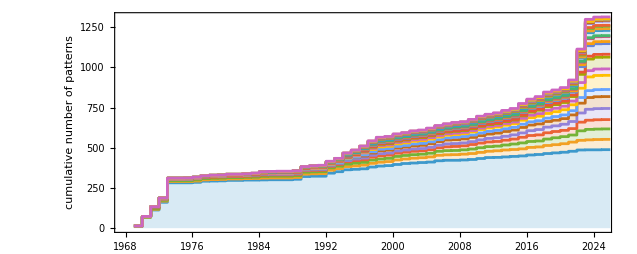

```mathematica
ListStepPlot[FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,BinCounts[#,{1,25,1}]&/@partsbydate]],PlotLayout->"Stacked",Filling->Table[i->If[i == 1, Axis, {i - 1}], {i, 1, 24}],Frame->True,PlotRange->All,AspectRatio->.4,(*PlotStyle->{Red,Automatic},*)FrameLabel->{None,"cumulative number of patterns"}]
```

```mathematica
Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,BinCounts[#,{1,25,1}]&/@partsbydate]]
```

{{{1969,14},{1970,54},{1971,45},{1972,48},{1973,121},{1975,0},{1976,3},{1977,7},{1978,1},{1979,1},{1980,3},{1982,2},{1983,0},{1984,1},{1985,1},{1986,0},{1988,3},{1989,17},{1990,2},{1991,0},{1992,19},{1993,9},{1994,12},{1995,3},{1996,3},{1997,11},{1998,6},{1999,3},{2000,7},{2001,6},{2002,3},{2003,3},{2004,3},{2005,8},{2006,3},{2007,0},{2008,2},{2009,3},{2010,6},{2011,6},{2012,1},{2013,3},{2014,3},{2015,3},{2016,6},{2017,3},{2018,6},{2019,4},{2020,4},{2021,6},{2022,8},{2023,1},{2024,0},{2025,1}},{{1969,0},{1970,0},{1971,4},{1972,3},{1973,1},{1975,0},{1976,0},{1977,0},{1978,1},{1979,0},{1980,0},{1982,0},{1983,1},{1984,1},{1985,0},{1986,0},{1988,0},{1989,4},{1990,0},{1991,1},{1992,2},{1993,1},{1994,1},{1995,1},{1996,2},{1997,0},{1998,1},{1999,1},{2000,3},{2001,0},{2002,2},{2003,0},{2004,2},{2005,2},{2006,0},{2007,1},{2008,1},{2009,1},{2010,1},{2011,1},{2012,2},{2013,2},{2014,0},{2015,1},{2016,3},{2017,0},{2018,3},{2019,1},{2020,2},{2021,4},{2022,3},{2023,2},{2024,2},{2025,0}},{{1969,0},{1970,1},{1971,2},{1972,2},{1973,0},{1975,0},{1976,2},{1977,1},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,3},{1985,0},{1986,0},{1988,0},{1989,1},{1990,0},{1991,0},{1992,3},{1993,0},{1994,0},{1995,2},{1996,0},{1997,3},{1998,0},{1999,0},{2000,2},{2001,0},{2002,0},{2003,0},{2004,1},{2005,2},{2006,1},{2007,0},{2008,1},{2009,1},{2010,1},{2011,0},{2012,0},{2013,2},{2014,3},{2015,3},{2016,0},{2017,0},{2018,3},{2019,3},{2020,1},{2021,0},{2022,15},{2023,6},{2024,0},{2025,0}},{{1969,0},{1970,3},{1971,3},{1972,1},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,1},{1984,0},{1985,0},{1986,0},{1988,0},{1989,1},{1990,0},{1991,0},{1992,0},{1993,2},{1994,4},{1995,1},{1996,0},{1997,2},{1998,2},{1999,0},{2000,0},{2001,0},{2002,1},{2003,0},{2004,1},{2005,0},{2006,2},{2007,1},{2008,0},{2009,3},{2010,1},{2011,0},{2012,0},{2013,1},{2014,1},{2015,4},{2016,2},{2017,1},{2018,1},{2019,0},{2020,0},{2021,1},{2022,14},{2023,3},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,2},{1972,0},{1973,0},{1975,0},{1976,0},{1977,1},{1978,1},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,1},{1994,2},{1995,3},{1996,1},{1997,1},{1998,1},{1999,0},{2000,1},{2001,0},{2002,0},{2003,0},{2004,1},{2005,1},{2006,2},{2007,0},{2008,0},{2009,0},{2010,2},{2011,2},{2012,1},{2013,1},{2014,2},{2015,1},{2016,3},{2017,3},{2018,2},{2019,0},{2020,3},{2021,6},{2022,13},{2023,11},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,1},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,1},{1982,0},{1983,0},{1984,2},{1985,0},{1986,0},{1988,0},{1989,0},{1990,1},{1991,0},{1992,0},{1993,0},{1994,1},{1995,2},{1996,4},{1997,2},{1998,4},{1999,0},{2000,0},{2001,0},{2002,1},{2003,1},{2004,2},{2005,0},{2006,2},{2007,0},{2008,1},{2009,1},{2010,0},{2011,1},{2012,2},{2013,1},{2014,0},{2015,4},{2016,1},{2017,0},{2018,0},{2019,0},{2020,0},{2021,6},{2022,20},{2023,12},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,1},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,1},{1995,1},{1996,4},{1997,1},{1998,2},{1999,0},{2000,0},{2001,0},{2002,2},{2003,0},{2004,0},{2005,0},{2006,1},{2007,2},{2008,0},{2009,0},{2010,2},{2011,0},{2012,0},{2013,0},{2014,0},{2015,3},{2016,0},{2017,0},{2018,1},{2019,2},{2020,0},{2021,3},{2022,9},{2023,8},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,1},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,1},{1988,0},{1989,1},{1990,0},{1991,0},{1992,1},{1993,2},{1994,2},{1995,1},{1996,4},{1997,1},{1998,0},{1999,0},{2000,2},{2001,0},{2002,1},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,2},{2010,2},{2011,0},{2012,0},{2013,1},{2014,0},{2015,3},{2016,1},{2017,2},{2018,1},{2019,1},{2020,2},{2021,5},{2022,21},{2023,27},{2024,3},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,1},{1985,0},{1986,0},{1988,0},{1989,0},{1990,1},{1991,0},{1992,0},{1993,0},{1994,1},{1995,0},{1996,1},{1997,3},{1998,2},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,1},{2012,0},{2013,1},{2014,0},{2015,1},{2016,3},{2017,1},{2018,4},{2019,1},{2020,1},{2021,1},{2022,12},{2023,4},{2024,1},{2025,0}},{{1969,0},{1970,1},{1971,1},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,1},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,0},{1995,2},{1996,1},{1997,1},{1998,0},{1999,0},{2000,1},{2001,1},{2002,1},{2003,0},{2004,1},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,1},{2014,0},{2015,3},{2016,4},{2017,2},{2018,1},{2019,1},{2020,0},{2021,5},{2022,23},{2023,21},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,1},{1995,0},{1996,2},{1997,1},{1998,1},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,0},{2014,0},{2015,0},{2016,2},{2017,0},{2018,2},{2019,0},{2020,0},{2021,0},{2022,5},{2023,4},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,1},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,1},{1982,0},{1983,1},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,1},{1994,1},{1995,0},{1996,1},{1997,0},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,1},{2004,0},{2005,2},{2006,0},{2007,2},{2008,0},{2009,0},{2010,1},{2011,1},{2012,1},{2013,0},{2014,1},{2015,0},{2016,0},{2017,2},{2018,0},{2019,0},{2020,0},{2021,1},{2022,16},{2023,31},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,2},{1995,0},{1996,1},{1997,1},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,1},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,0},{2014,0},{2015,0},{2016,0},{2017,2},{2018,0},{2019,0},{2020,0},{2021,1},{2022,4},{2023,1},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,1},{1990,0},{1991,1},{1992,0},{1993,0},{1994,0},{1995,0},{1996,0},{1997,1},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,1},{2013,0},{2014,0},{2015,0},{2016,1},{2017,0},{2018,1},{2019,0},{2020,0},{2021,4},{2022,5},{2023,16},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,1},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,1},{1990,0},{1991,0},{1992,0},{1993,0},{1994,0},{1995,0},{1996,0},{1997,0},{1998,0},{1999,0},{2000,0},{2001,1},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,1},{2011,0},{2012,0},{2013,0},{2014,0},{2015,0},{2016,0},{2017,0},{2018,1},{2019,0},{2020,0},{2021,0},{2022,1},{2023,0},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,1},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,2},{1995,0},{1996,0},{1997,2},{1998,0},{1999,1},{2000,0},{2001,0},{2002,0},{2003,0},{2004,1},{2005,0},{2006,0},{2007,1},{2008,0},{2009,2},{2010,0},{2011,0},{2012,1},{2013,0},{2014,1},{2015,0},{2016,1},{2017,0},{2018,1},{2019,0},{2020,0},{2021,3},{2022,3},{2023,11},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,1},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,2},{1994,2},{1995,0},{1996,0},{1997,1},{1998,1},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,0},{2014,0},{2015,0},{2016,0},{2017,0},{2018,0},{2019,0},{2020,0},{2021,0},{2022,0},{2023,4},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,1},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,0},{1995,0},{1996,0},{1997,0},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,0},{2014,1},{2015,1},{2016,0},{2017,0},{2018,0},{2019,0},{2020,0},{2021,0},{2022,9},{2023,3},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,1},{1991,0},{1992,0},{1993,0},{1994,0},{1995,0},{1996,0},{1997,0},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,1},{2010,1},{2011,0},{2012,0},{2013,0},{2014,0},{2015,1},{2016,0},{2017,0},{2018,0},{2019,0},{2020,0},{2021,1},{2022,1},{2023,0},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,0},{1995,1},{1996,1},{1997,0},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,1},{2011,0},{2012,0},{2013,0},{2014,0},{2015,1},{2016,0},{2017,0},{2018,1},{2019,0},{2020,1},{2021,0},{2022,5},{2023,14},{2024,1},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,1},{1995,1},{1996,0},{1997,0},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,1},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,0},{2014,0},{2015,1},{2016,0},{2017,0},{2018,0},{2019,0},{2020,0},{2021,0},{2022,1},{2023,0},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,1},{1992,0},{1993,0},{1994,0},{1995,0},{1996,0},{1997,0},{1998,2},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,0},{2014,0},{2015,0},{2016,0},{2017,0},{2018,0},{2019,0},{2020,0},{2021,0},{2022,2},{2023,2},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,1},{1995,0},{1996,0},{1997,0},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,0},{2011,0},{2012,0},{2013,0},{2014,0},{2015,0},{2016,0},{2017,0},{2018,0},{2019,0},{2020,0},{2021,0},{2022,0},{2023,0},{2024,0},{2025,0}},{{1969,0},{1970,0},{1971,0},{1972,0},{1973,0},{1975,0},{1976,0},{1977,0},{1978,0},{1979,0},{1980,0},{1982,0},{1983,1},{1984,0},{1985,0},{1986,0},{1988,0},{1989,0},{1990,0},{1991,0},{1992,0},{1993,0},{1994,0},{1995,0},{1996,0},{1997,1},{1998,0},{1999,0},{2000,0},{2001,0},{2002,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0},{2008,0},{2009,0},{2010,1},{2011,0},{2012,0},{2013,2},{2014,0},{2015,1},{2016,0},{2017,0},{2018,0},{2019,0},{2020,1},{2021,0},{2022,2},{2023,4},{2024,0},{2025,0}}}